## Моделирование вывода лекарства на рынок

### Стандартная модель

```mathematica
Clear["Global`*"]
c={6,6.05,6.1};
n={802000,967000,1132000};
v=c*n;
s=0.55*v;
vp=v-s;
op=0.15 vp;
cd=vp-op;
ng=0.32 cd;
cf=cd-ng;
NPV=TimeValue[Cashflow[Prepend[cf,-3400000]],0.10,0]
IRR=irr/.FindRoot[
TimeValue[Cashflow[Prepend[cf,-3400000]],irr,0]==0,
{irr,0.15}]
```

344796.

0.153314

### Модель методом монте-карло

```mathematica
Clear["Global`*"]
ts=SessionTime[];
Ftr[min_,cnt_,max_]:=RandomVariate[TriangularDistribution[{min,max},cnt]]
Fnorm[cnt_,sig_]:=RandomVariate[NormalDistribution[cnt,sig]]

tn=10;

c=Transpose[{
Array [Ftr[5.9,6,6.1]&,tn],
Array [Ftr[5.95,6.05,6.15]&,tn],
Array [Ftr[6.0,6.1,6.2]&,tn]
}];
n=Transpose[{
Array [Fnorm[802000,25000]&,tn],
Array [Fnorm[967000,30000]&,tn],
Array [Fnorm[1132000,25000]&,tn]
}];
v=c*n;
s=Array [Ftr[0.5,0.55,0.65]&,{tn,3}]*v;
vp=v-s;
op=Array [Fnorm[0.15,0.02]&,{tn,3}]*vp;
cd=vp-op;
ng=0.32 cd;
cf=cd-ng;
cff=Prepend[#,-3400000]&/@ cf;
NPV=TimeValue[Cashflow[#],0.10,0]&/@ cff
IRR=irr/.FindRoot[TimeValue[Cashflow[#],irr,0]==0,{irr,0.15}]&/@ cff
SessionTime[]-ts
```

{192942.,205711.,153244.,300738.,-33956.4,227009.,346389.,78144.5,230503.,155446.}

{0.13082,0.131763,0.124395,0.145464,0.0945787,0.135977,0.153572,0.112663,0.136204,0.123783}

0.13789

{209976.,252828.,45826.9,82963.1,245197.,-99566.3,419552.,206877.,214814.,309426.}

{0.132835,0.139078,0.107495,0.112677,0.137866,0.0840165,0.164523,0.132152,0.132966,0.147933}

0.01737

#### Итог

```mathematica
Clear["Global`*"]
ts=SessionTime[];
Ftr[min_,cnt_,max_]:=RandomVariate[TriangularDistribution[{min,max},cnt]]
Fnorm[cnt_,sig_]:=RandomVariate[NormalDistribution[cnt,sig]]


tn=10000;


c=Transpose[{
Array [Ftr[5.9,6,6.1]&,tn],
Array [Ftr[5.95,6.05,6.15]&,tn],
Array [Ftr[6.0,6.1,6.2]&,tn]
}];
n=Transpose[{
Array [Fnorm[802000,25000]&,tn],
Array [Fnorm[967000,30000]&,tn],
Array [Fnorm[1132000,25000]&,tn]
}];
v=c*n;
s=Array [Ftr[0.5,0.55,0.65]&,{tn,3}]*v;
vp=v-s;
op=Array [Fnorm[0.15,0.02]&,{tn,3}]*vp;
cd=vp-op;
ng=0.32 cd;
cf=cd-ng;
cff=Prepend[#,-3400000]&/@ cf;
NPV=TimeValue[Cashflow[#],0.10,0]&/@ cff;
IRR=irr/.FindRoot[TimeValue[Cashflow[#],irr,0]==0,{irr,0.15}]&/@ cff;
SessionTime[]-ts
```

59.29128

----------------------------------------

NPV 205183.     IRR 0.131721

Вероятность отриц. NPV 0.1186

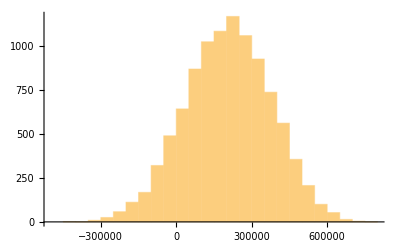

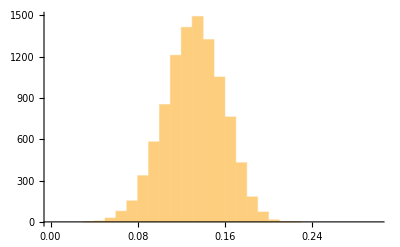

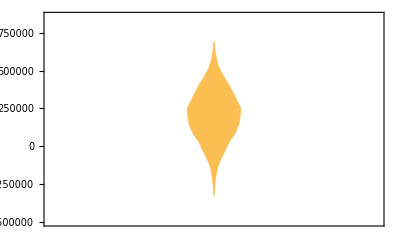

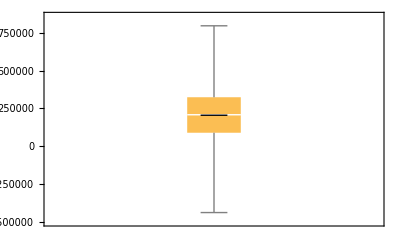

| Min | Mean | Max
NPV | -438725. | 205183. | 796906.
IRR | 0.03005 | 0.131721 | 0.220413

| P10 | P50 | P90
NPV | -19275. | 208420. | 423883.
IRR | 0.0969871 | 0.132388 | 0.165417

| Q 1/4 | Q 1/2 | Q 3/4
NPV | 89372.8 | 208420. | 324179.
IRR | 0.114027 | 0.132388 | 0.150149

```mathematica
Print["----------------------------------------"]
Print[" "]
Print["NPV ",Mean[NPV],"     IRR ",Mean[IRR]]
Print["Вероятность отриц. NPV ",Length[Select[NPV,#≤ 0&]]/tn*1.]

Histogram[NPV,{-500000,800000,50000}]
Histogram[IRR,{0,0.3,0.01}]
DistributionChart[NPV]
BoxWhiskerChart[NPV,"Mean"]


Grid[{
{" ","Min","Mean","Max"},
{"NPV",Min[NPV],Mean[NPV],Max[NPV]},
{"IRR",Min[IRR],Mean[IRR],Max[IRR]}
},Frame->All]

Grid[{
{" ","P10","P50","P90"},
Flatten[{"NPV",Quantile[NPV,{1/10,1/2,9/10},{{1/2, 0}, {0, 1}}]}],
Flatten[{"IRR",Quantile[IRR,{1/10,1/2,9/10},{{1/2, 0}, {0, 1}}]}]
},Frame->All]

Grid[{
{" ","Q 1/4","Q 1/2","Q 3/4"},
Flatten[{"NPV",Quartiles[NPV]}],
Flatten[{"IRR",Quartiles[IRR]}]
},Frame->All]
```